# Lattice Simulation

## Bloch wave basis, periodic potential

#### Dispersion relation

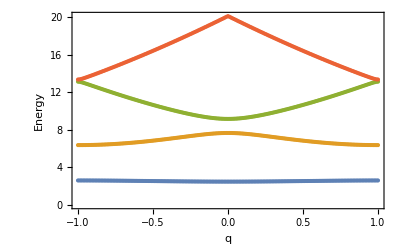

```mathematica
Hij[V0_,q_,i_,j_]:=If[i==j,(2i+q)^2+V0/2,If[Abs[i-j]==1,-1/4 V0,0]]; (*Hamiltonian matrix elements*)
lMax=50;  (*maximum absolute value of bloch wave index*)
H[V0_,q_]:=Table[Hij[V0,q,i,j],{i,-lMax,lMax},{j,-lMax,lMax}] (* Hamiltonian matrix form *)
eigenvals[V_,q_]:=Sort[N[Eigenvalues[H[V,q]]]] (* Get eigenvalues of matrix (eigenenergies) *)
V0=8;
qlist=Range[-1,1,0.01];(*quasi-momentum list from -q0 to q0*)
EnergyMx=Map[eigenvals[V0,#]&,qlist];(* list of lists: energy eigenvalues for each quasi momentum value q *)
nband=4;(*Plot to nth band, which should be smaller than (2*lmax+1)*)
FigBS2=ListPlot[Table[Transpose[{qlist,EnergyMx[[All,iband]]}],{iband,1,nband}],Frame->True,FrameLabel->{"q","Energy"}](*listplot is fast*)
```

#### Band Gaps

```mathematica
BandGapMin=Table[Min[EnergyMx[[All,jband]]-EnergyMx[[All,1]]],{jband,2,nband}];(*min band gap 1-2, 1-3, 1-4, ... till 1-nband *)
BandGapMax=Table[Max[EnergyMx[[All,jband]]-EnergyMx[[All,1]]],{jband,2,nband}];(*max band gap ..*)
BandGapMean=Table[Mean[EnergyMx[[All,jband]]-EnergyMx[[All,1]]],{jband,2,nband}];(*mean band gap ..*)
BandGapTb=Transpose[{BandGapMin,BandGapMax,BandGapMean}];
FirstColumn = Prepend[Table["1-"<>ToString[j],{j,2,nband}],"Band Gap"];
DataColumns = Prepend[BandGapTb,{"Min","Max","Mean"}];
BandGapTbLabel=MapThread[Prepend,{DataColumns,FirstColumn}];
Grid[BandGapTbLabel,Dividers->{False,All}]
```

Band Gap | Min | Max | Mean
1-2 | 3.76988 | 5.18619 | 4.38201
1-3 | 6.68662 | 10.5313 | 8.2857
1-4 | 10.761 | 17.6416 | 13.9606

#### Tunneling

```mathematica
BandMax=Map[Max[EnergyMx[[All,#]]]&,Range[1,nband]]; (* max energy for each band *)
BandMin=Map[Min[EnergyMx[[All,#]]]&,Range[1,nband]];(* min energy for each band *)
BandWidth = BandMax-BandMin;(* band width for each band *)
Tunneling=BandWidth/4; (* saw in Dieter Jaksch PRL paper 1998, which is valid both for all bands if the band is deep enough such as 5Er*)
FirstColumn = Prepend[Table["Band"<>ToString[j],{j,1,nband}]," "];
DataColumns = Prepend[Tunneling,"Tunneling"];
BWColumn = Prepend[BandWidth, "Bandwidth"];
Grid[Transpose[{FirstColumn,DataColumns, BWColumn}],Dividers->{False,All}]
```

| Tunneling | Bandwidth
Band1 | 0.0308201 | 0.12328
Band2 | 0.323258 | 1.29303
Band3 | 0.991991 | 3.96796
Band4 | 1.68934 | 6.75737

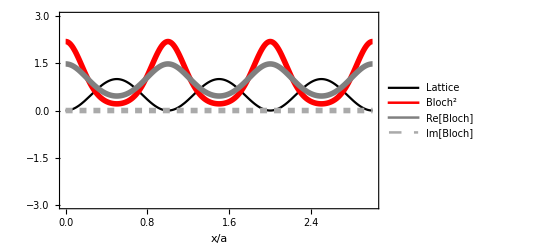
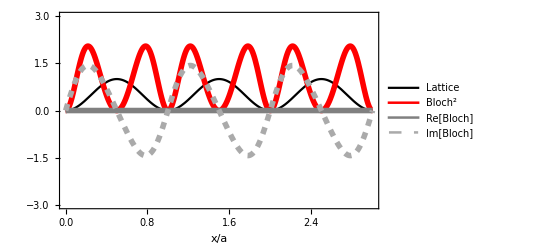

```mathematica
EV[V_,q_,l_]:=Sort[Transpose[Chop[N[Eigensystem[H[V,q]]]]]] [[l,2]]; (* Get the l th eigen vector of H *)
EVNormed[V_,q_,l_]:=Module[{tmp=EV[V,q,l]},(tmp/Norm[tmp])] ; (* Get normed l th eigen vector of H *)
Bloch[x_,V_,q_,l_]:=Sum[Exp[π*I (q+2n) x]*EVNormed[V,q,l][[n+lMax+1]],{n,-lMax,lMax}];(*should we use cutoff jMax or smaller one instead??*)
BRe[x_]={Re[ Bloch[x,V0,0,1]],Re[ Bloch[x,V0,0,2]]};
BIm[x_]={Im[ Bloch[x,V0,0,1]],Im[ Bloch[x,V0,0,2]]};
BNorm[x_]={Re[ Bloch[x,V0,0,1]],Re[I Bloch[x,V0,0,2]]};
Table[Plot[{Sin[π*x]^2,(BNorm[x]^2)[[i]],BRe[x][[i]],BIm[x][[i]]},{x,0,3},Frame->True,Axes->False,FrameLabel->{"x/a"},PlotRange->{-3,3},PlotLegends->{"Lattice","Bloch^2","Re[Bloch]","Im[Bloch]"},PlotStyle->{{Thick,Black},{Thickness[0.01],Red},{Thickness[0.01],Gray},{Thickness[0.01],Dashed,Lighter[Gray]}}],{i,1,2}]
```

### Wannier Funcs

```mathematica
Note1: Ref. W. Kohn. Analytic properties of bloch waves and wannier functions (1959).
Note2: Even though the sum of Bloch[q] and Bloch[-q] is either real or imaginary, wannier function cannot be  calculated by summing Bloch waves up simply with the phase factor like  ⅈ + or -. We do need the phasefactor function.
```

```mathematica
PhaseFactor[V_,q_,l_]:=If[OddQ[l],Arg[Bloch[0,V,q,l]],Arg[Bloch[0.25,V,q,l]]];(*force phase at x=0 equals to 0 for every Bloch waves for odd band and phase at x=0.25 (or values close to 0.13) equals to 0 for even band. It just Works!!*)
qqstep=0.1;
Wannier[x_,V_,l_,xi_]:=Sum[Exp[π*I*q*(-xi)]*Exp[-I*PhaseFactor[V,q,l]]*Bloch[x,V,q,l],{q,-1,1,qqstep}]*(qqstep/2)-1/2(Sum[Exp[π*I*q*(-xi)]*Exp[-I*PhaseFactor[V,q,l]]*Bloch[x,V,q,l],{q,-1,1,2}])*(qqstep/2);
nWannier=2;(*1st, 2nd, 3rd band*)
xxstep=0.01;xlist=Range[-5,5,xxstep];
wlist = Wannier[xlist,Vlat,nWannier,0];
ltslist=Sin[π*xlist]^2;(*lattice potential*)
wlistNorm=wlist/√Total[Re[wlist]^2*xxstep];(*Normalize the wannier function. Here wannier function is assumed to be real*)
ListPlot[{Transpose[{xlist,ltslist}],Transpose[{xlist,Re[wlistNorm]^2}],Transpose[{xlist,Re[wlistNorm]}],Transpose[{xlist,Im[wlistNorm]}]},FrameLabel->{"x/a"},Frame->True,PlotLegends->{"Lattice","Wannier^2","Re[Wannier]","Im[Wannier]"},PlotStyle->{{Thick,Black},{Thickness[0.01],Red},{Thickness[0.01],Gray},{Thickness[0.01],Dashed,Lighter[Gray]}}]
```

## Bloch wave basis, periodic potential + linear term

#### Dispersion relation